# Project Euler Problem 74

```mathematica
Clear[digitFactorialSum];
digitFactorialSum[{d_}] := digitFactorialSum[{d}] = d!
digitFactorialSum[{d_, rest__}] := digitFactorialSum[{d, rest}] = d! + digitFactorialSum[{rest}]
digitFactorialSum[d_Integer] := digitFactorialSum[Sort[IntegerDigits[d]]]

lastMemberMostQ[most___, last_] := MemberQ[{most}, last]
digitFactorialSumCycle[n_] := NestWhileList[digitFactorialSum, n, Not @* lastMemberMostQ, All]
digitFactorialSumCycleLength[n_] := Length[digitFactorialSumCycle[n]] - 1

Clear[digitFactorialSumCycleLength];
digitFactorialSumCycleLength[digits_List] := digitFactorialSumCycleLength[digits] = Length[digitFactorialSumCycle[digits]] - 1
digitFactorialSumCycleLength[n_Integer] := digitFactorialSumCycleLength[Sort[IntegerDigits[n]]]
```

```mathematica
cycleLengths=Table[digitFactorialSumCycleLength[k],{k,10^6-1}];
```

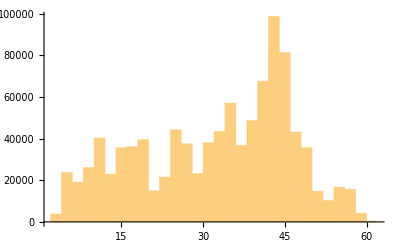

```mathematica
Histogram[cycleLengths]
```

```mathematica
Count[cycleLengths,60]
```

402